```mathematica
ClearAll["Global`*"]
```

### Pion

```mathematica
idealπ=
{{7.17752430*10^-03,2.01939637*10^+02},{3.78993630*10^-02,2.02051375*10^+02},{9.35073360*10^-02,1.98657813*10^+02},{1.74611500*10^-01,1.77252617*10^+02},{2.82124830*10^-01,1.35205960*10^+02},{4.17333600*10^-01,8.95559489*10^+01},{5.81993540*10^-01,5.30861632*10^+01},{7.78479140*10^-01,2.86070980*10^+01},{1.01002170*10^+00,1.40323350*10^+01},{1.28110830*10^+00,6.20952680*10^+00},{1.59819070*10^+00,2.43629368*10^+00},{1.97106870*10^+00,8.24511217*10^-01},{2.41596300*10^+00,2.30044631*10^-01},{2.96389860*10^+00,4.85663778*10^-02}};


shear14π={{7.17752430*10^-03,2.02445071*10^+02},{3.78993630*10^-02,2.02377534*10^+02},{9.35073360*10^-02,1.98289128*10^+02},{1.74611500*10^-01,1.76000649*10^+02},{2.82124830*10^-01,1.33634031*10^+02},{4.17333600*10^-01,8.82585568*10^+01},{5.81993540*10^-01,5.22870918*10^+01},{7.78479140*10^-01,2.82665140*10^+01},{1.01002170*10^+00,1.39995020*10^+01},{1.28110830*10^+00,6.31953648*10^+00},{1.59819070*10^+00,2.56818609*10^+00},{1.97106870*10^+00,9.19878476*10^-01},{2.41596300*10^+00,2.79799342*10^-01},{2.96389860*10^+00,6.71023520*10^-02}};

shearCEπ=
{{7.17752430*10^-03,2.04618817*10^+02},{3.78993630*10^-02,2.03709717*10^+02},{9.35073360*10^-02,1.96683595*10^+02},{1.74611500*10^-01,1.71844882*10^+02},{2.82124830*10^-01,1.29954179*10^+02},{4.17333600*10^-01,8.63335201*10^+01},{5.81993540*10^-01,5.17501190*10^+01},{7.78479140*10^-01,2.84258383*10^+01},{1.01002170*10^+00,1.43445251*10^+01},{1.28110830*10^+00,6.59918977*10^+00},{1.59819070*10^+00,2.72277175*10^+00},{1.97106870*10^+00,9.80927868*10^-01},{2.41596300*10^+00,2.95256790*10^-01},{2.96389860*10^+00,6.83362003*10^-02}};

shearmodπ ={{7.17752430*10^-03,2.04620236*10^+02},{3.78993630*10^-02,2.03981201*10^+02},{9.35073360*10^-02,1.97787507*10^+02},{1.74611500*10^-01,1.73266292*10^+02},{2.82124830*10^-01,1.30625292*10^+02},{4.17333600*10^-01,8.61800001*10^+01},{5.81993540*10^-01,5.11970737*10^+01},{7.78479140*10^-01,2.78299730*10^+01},{1.01002170*10^+00,1.38837625*10^+01},{1.28110830*10^+00,6.31389923*10^+00},{1.59819070*10^+00,2.57918871*10^+00},{1.97106870*10^+00,9.23756477*10^-01},{2.41596300*10^+00,2.78629357*10^-01},{2.96389860*10^+00,6.55571012*10^-02}};


bulk14π = {{7.17752430*10^-03,1.90663757*10^+02},{3.78993630*10^-02,1.90801591*10^+02},{9.35073360*10^-02,1.87244966*10^+02},{1.74611500*10^-01,1.64666848*10^+02},{2.82124830*10^-01,1.21028378*10^+02},{4.17333600*10^-01,7.52137106*10^+01},{5.81993540*10^-01,4.05033741*10^+01},{7.78479140*10^-01,1.88969500*10^+01},{1.01002170*10^+00,7.34873516*10^+00},{1.28110830*10^+00,2.10367891*10^+00},{1.59819070*10^+00,2.11287661*10^-01},{1.97106870*10^+00,-2.14615700*10^-01},{2.41596300*10^+00,-1.71729067*10^-01},{2.96389860*10^+00,-7.05821422*10^-02}};

bulkCEπ=
{{7.17752430*10^-03,1.77283821*10^+02},{3.78993630*10^-02,1.77624273*10^+02},{9.35073360*10^-02,1.73440953*10^+02},{1.74611500*10^-01,1.45851047*10^+02},{2.82124830*10^-01,9.77398374*10^+01},{4.17333600*10^-01,5.40536937*10^+01},{5.81993540*10^-01,2.54474196*10^+01},{7.78479140*10^-01,9.98184194*10^+00},{1.01002170*10^+00,2.89646926*10^+00},{1.28110830*10^+00,2.84465526*10^-01},{1.59819070*10^+00,-3.37713798*10^-01},{1.97106870*10^+00,-2.91367642*10^-01},{2.41596300*10^+00,-1.39843624*10^-01},{2.96389860*10^+00,-4.46592663*10^-02}};

bulkmodπ=
{{7.17752430*10^-03,1.62720175*10^+02},{3.78993630*10^-02,1.63038290*10^+02},{9.35073360*10^-02,1.58737994*10^+02},{1.74611500*10^-01,1.30552524*10^+02},{2.82124830*10^-01,8.48545002*10^+01},{4.17333600*10^-01,4.66730857*10^+01},{5.81993540*10^-01,2.27184465*10^+01},{7.78479140*10^-01,9.87132987*10^+00},{1.01002170*10^+00,3.79617023*10^+00},{1.28110830*10^+00,1.26952323*10^+00},{1.59819070*10^+00,3.59847784*10^-01},{1.97106870*10^+00,8.32472824*10^-02},{2.41596300*10^+00,1.47829113*10^-02},{2.96389860*10^+00,1.79361039*10^-03}};

shearbulk14π={{7.17752430*10^-03,1.91169190*10^+02},{3.78993630*10^-02,1.91127749*10^+02},{9.35073360*10^-02,1.86876281*10^+02},{1.74611500*10^-01,1.63414880*10^+02},{2.82124830*10^-01,1.19456448*10^+02},{4.17333600*10^-01,7.39163185*10^+01},{5.81993540*10^-01,3.97043027*10^+01},{7.78479140*10^-01,1.85563660*10^+01},{1.01002170*10^+00,7.31590211*10^+00},{1.28110830*10^+00,2.21368859*10^+00},{1.59819070*10^+00,3.43180073*10^-01},{1.97106870*10^+00,-1.19248441*10^-01},{2.41596300*10^+00,-1.21974356*10^-01},{2.96389860*10^+00,-5.20461680*10^-02}};

shearbulkCEπ={{7.17752430*10^-03,1.79963000*10^+02},{3.78993630*10^-02,1.79282614*10^+02},{9.35073360*10^-02,1.71466735*10^+02},{1.74611500*10^-01,1.40443313*10^+02},{2.82124830*10^-01,9.24880559*10^+01},{4.17333600*10^-01,5.08312650*10^+01},{5.81993540*10^-01,2.41113755*10^+01},{7.78479140*10^-01,9.80058224*10^+00},{1.01002170*10^+00,3.20865934*10^+00},{1.28110830*10^+00,6.74128495*10^-01},{1.59819070*10^+00,-5.12357307*10^-02},{1.97106870*10^+00,-1.34950992*10^-01},{2.41596300*10^+00,-7.46314658*10^-02},{2.96389860*10^+00,-2.48894438*10^-02}};

shearbulkmodπ={{7.17752430*10^-03,1.66511096*10^+02},{3.78993630*10^-02,1.65710031*10^+02},{9.35073360*10^-02,1.57196657*10^+02},{1.74611500*10^-01,1.25407351*10^+02},{2.82124830*10^-01,8.07966121*10^+01},{4.17333600*10^-01,4.47920748*10^+01},{5.81993540*10^-01,2.22718844*10^+01},{7.78479140*10^-01,1.00586660*10^+01},{1.01002170*10^+00,4.10620380*10^+00},{1.28110830*10^+00,1.49510448*10^+00},{1.59819070*10^+00,4.75813682*10^-01},{1.97106870*10^+00,1.28374101*10^-01},{2.41596300*10^+00,2.79361504*10^-02},{2.96389860*10^+00,4.45269816*10^-03}};
```

### Kaon

```mathematica
idealK={{7.17752430*10^-03,1.75867096*10^+01},{3.78993630*10^-02,1.75995793*10^+01},{9.35073360*10^-02,1.76562427*10^+01},{1.74611500*10^-01,1.77085946*10^+01},{2.82124830*10^-01,1.73819912*10^+01},{4.17333600*10^-01,1.59580463*10^+01},{5.81993540*10^-01,1.30667548*10^+01},{7.78479140*10^-01,9.28662014*10^+00},{1.01002170*10^+00,5.68208947*10^+00},{1.28110830*10^+00,2.98682032*10^+00},{1.59819070*10^+00,1.34023483*10^+00},{1.97106870*10^+00,5.04417395*10^-01},{2.41596300*10^+00,1.53382183*10^-01},{2.96389860*10^+00,3.47976324*10^-02}};

shear14K = {{7.17752430*10^-03,1.78367162*10^+01},{3.78993630*10^-02,1.78413474*10^+01},{9.35073360*10^-02,1.78572081*10^+01},{1.74611500*10^-01,1.78049306*10^+01},{2.82124830*10^-01,1.73099910*10^+01},{4.17333600*10^-01,1.57207265*10^+01},{5.81993540*10^-01,1.27611888*10^+01},{7.78479140*10^-01,9.03833300*10^+00},{1.01002170*10^+00,5.55678720*10^+00},{1.28110830*10^+00,2.96990245*10^+00},{1.59819070*10^+00,1.37758337*10^+00},{1.97106870*10^+00,5.48294569*10^-01},{2.41596300*10^+00,1.81834375*10^-01},{2.96389860*10^+00,4.69412811*10^-02}};

shearCEK={{7.17752430*10^-03,1.80924759*10^+01},{3.78993630*10^-02,1.80899351*10^+01},{9.35073360*10^-02,1.80700688*10^+01},{1.74611500*10^-01,1.79220831*10^+01},{2.82124830*10^-01,1.72626330*10^+01},{4.17333600*10^-01,1.55103134*10^+01},{5.81993540*10^-01,1.25103101*10^+01},{7.78479140*10^-01,8.88653546*10^+00},{1.01002170*10^+00,5.53313819*10^+00},{1.28110830*10^+00,3.01291985*10^+00},{1.59819070*10^+00,1.42354508*10^+00},{1.97106870*10^+00,5.72741594*10^-01},{2.41596300*10^+00,1.88967319*10^-01},{2.96389860*10^+00,4.73064304*10^-02}};

shearmodK={{7.17752430*10^-03,1.81131043*10^+01},{3.78993630*10^-02,1.81142967*10^+01},{9.35073360*10^-02,1.81125908*10^+01},{1.74611500*10^-01,1.80087596*10^+01},{2.82124830*10^-01,1.74086954*10^+01},{4.17333600*10^-01,1.56804431*10^+01},{5.81993540*10^-01,1.26245661*10^+01},{7.78479140*10^-01,8.89681175*10^+00},{1.01002170*10^+00,5.46613884*10^+00},{1.28110830*10^+00,2.92842647*10^+00},{1.59819070*10^+00,1.36164980*10^+00},{1.97106870*10^+00,5.41220792*10^-01},{2.41596300*10^+00,1.77885957*10^-01},{2.96389860*10^+00,4.50348138*10^-02}};

bulk14K = {{7.17752430*10^-03,1.72624313*10^+01},{3.78993630*10^-02,1.72801653*10^+01},{9.35073360*10^-02,1.73592246*10^+01},{1.74611500*10^-01,1.74492698*10^+01},{2.82124830*10^-01,1.71017534*10^+01},{4.17333600*10^-01,1.54642488*10^+01},{5.81993540*10^-01,1.21540351*10^+01},{7.78479140*10^-01,7.96716718*10^+00},{1.01002170*10^+00,4.22331009*10^+00},{1.28110830*10^+00,1.71618622*10^+00},{1.59819070*10^+00,4.48730514*10^-01},{1.97106870*10^+00,-1.24027594*10^-03},{2.41596300*10^+00,-7.37178900*10^-02},{2.96389860*10^+00,-4.10798681*10^-02}};

bulkCEK={{7.17752430*10^-03,1.88375634*10^+01},{3.78993630*10^-02,1.88617852*10^+01},{9.35073360*10^-02,1.89725917*10^+01},{1.74611500*10^-01,1.91313432*10^+01},{2.82124830*10^-01,1.88206317*10^+01},{4.17333600*10^-01,1.69835237*10^+01},{5.81993540*10^-01,1.31187434*10^+01},{7.78479140*10^-01,8.28351537*10^+00},{1.01002170*10^+00,4.16018854*10^+00},{1.28110830*10^+00,1.59332710*10^+00},{1.59819070*10^+00,4.04622074*10^-01},{1.97106870*10^+00,1.90932224*10^-02},{2.41596300*10^+00,-4.06414694*10^-02},{2.96389860*10^+00,-2.16839795*10^-02}};

bulkmodK={{7.17752430*10^-03,1.94148234*10^+01},{3.78993630*10^-02,1.94416140*10^+01},{9.35073360*10^-02,1.95705162*10^+01},{1.74611500*10^-01,1.98081286*10^+01},{2.82124830*10^-01,1.96672097*10^+01},{4.17333600*10^-01,1.77903604*10^+01},{5.81993540*10^-01,1.32834405*10^+01},{7.78479140*10^-01,7.78036080*10^+00},{1.01002170*10^+00,3.60911521*10^+00},{1.28110830*10^+00,1.35388721*10^+00},{1.59819070*10^+00,4.12097892*10^-01},{1.97106870*10^+00,9.97434075*10^-02},{2.41596300*10^+00,1.82410085*10^-02},{2.96389860*10^+00,2.25723137*10^-03}};

shearbulk14K = {{7.17752430*10^-03,1.75124378*10^+01},{3.78993630*10^-02,1.75219334*10^+01},{9.35073360*10^-02,1.75601900*10^+01},{1.74611500*10^-01,1.75456058*10^+01},{2.82124830*10^-01,1.70297532*10^+01},{4.17333600*10^-01,1.52269291*10^+01},{5.81993540*10^-01,1.18484690*10^+01},{7.78479140*10^-01,7.71888003*10^+00},{1.01002170*10^+00,4.09800782*10^+00},{1.28110830*10^+00,1.69926835*10^+00},{1.59819070*10^+00,4.86079050*10^-01},{1.97106870*10^+00,4.26368978*10^-02},{2.41596300*10^+00,-4.52656980*10^-02},{2.96389860*10^+00,-2.89362194*10^-02}};

shearbulkCEK={{7.17752430*10^-03,1.93433296*10^+01},{3.78993630*10^-02,1.93521411*10^+01},{9.35073360*10^-02,1.93864179*10^+01},{1.74611500*10^-01,1.93448317*10^+01},{2.82124830*10^-01,1.87012735*10^+01},{4.17333600*10^-01,1.65357909*10^+01},{5.81993540*10^-01,1.25622988*10^+01},{7.78479140*10^-01,7.88343069*10^+00},{1.01002170*10^+00,4.01123726*10^+00},{1.28110830*10^+00,1.61942663*10^+00},{1.59819070*10^+00,4.87932326*10^-01},{1.97106870*10^+00,8.74174214*10^-02},{2.41596300*10^+00,-5.05633279*10^-03},{2.96389860*10^+00,-9.17518153*10^-03},{3.69431420*10^+00,-2.58624404*10^-03}};

shearbulkmodK = {{7.17752430*10^-03,2.01525561*10^+01},{3.78993630*10^-02,2.01763948*10^+01},{9.35073360*10^-02,2.02784266*10^+01},{1.74611500*10^-01,2.03924501*10^+01},{2.82124830*10^-01,1.98792549*10^+01},{4.17333600*10^-01,1.74427745*10^+01},{5.81993540*10^-01,1.27509694*10^+01},{7.78479140*10^-01,7.55759721*10^+00},{1.01002170*10^+00,3.68607652*10^+00},{1.28110830*10^+00,1.50602649*10^+00},{1.59819070*10^+00,5.17329040*10^-01},{1.97106870*10^+00,1.47071088*10^-01},{2.41596300*10^+00,3.31998668*10^-02},{2.96389860*10^+00,5.43305491*10^-03}};
```

### Proton

```mathematica
idealp={{7.17752430*10^-03,1.76325959*10^+00},{3.78993630*10^-02,1.76425600*10^+00},{9.35073360*10^-02,1.76954193*10^+00},{1.74611500*10^-01,1.78383528*10^+00},{2.82124830*10^-01,1.80804081*10^+00},{4.17333600*10^-01,1.82712977*10^+00},{5.81993540*10^-01,1.79649471*10^+00},{7.78479140*10^-01,1.65075437*10^+00},{1.01002170*10^+00,1.35483385*10^+00},{1.28110830*10^+00,9.55849805*10^-01},{1.59819070*10^+00,5.63169135*10^-01},{1.97106870*10^+00,2.69865428*10^-01},{2.41596300*10^+00,1.01315125*10^-01},{2.96389860*10^+00,2.76614013*10^-02}};

shear14p ={{7.17752430*10^-03,1.82139067*10^+00},{3.78993630*10^-02,1.82200846*10^+00},{9.35073360*10^-02,1.82542580*10^+00},{1.74611500*10^-01,1.83421655*10^+00},{2.82124830*10^-01,1.84603935*10^+00},{4.17333600*10^-01,1.84258072*10^+00},{5.81993540*10^-01,1.78042328*10^+00},{7.78479140*10^-01,1.60553119*10^+00},{1.01002170*10^+00,1.29976806*10^+00},{1.28110830*10^+00,9.15879395*10^-01},{1.59819070*10^+00,5.49794718*10^-01},{1.97106870*10^+00,2.75919045*10^-01},{2.41596300*10^+00,1.12486478*10^-01},{2.96389860*10^+00,3.49862653*10^-02}};

shearCEp={{7.17752430*10^-03,1.83000332*10^+00},{3.78993630*10^-02,1.83062304*10^+00},{9.35073360*10^-02,1.83404739*10^+00},{1.74611500*10^-01,1.84273280*10^+00},{2.82124830*10^-01,1.85372928*10^+00},{4.17333600*10^-01,1.84730854*10^+00},{5.81993540*10^-01,1.77908742*10^+00},{7.78479140*10^-01,1.59780930*10^+00},{1.01002170*10^+00,1.29132803*10^+00},{1.28110830*10^+00,9.13430782*10^-01},{1.59819070*10^+00,5.53277411*10^-01},{1.97106870*10^+00,2.80038789*10^-01},{2.41596300*10^+00,1.13951463*10^-01},{2.96389860*10^+00,3.45743327*10^-02}};

shearmodp={{7.17752430*10^-03,1.83626535*10^+00},{3.78993630*10^-02,1.83694456*10^+00},{9.35073360*10^-02,1.84080584*10^+00},{1.74611500*10^-01,1.85087526*10^+00},{2.82124830*10^-01,1.86493425*10^+00},{4.17333600*10^-01,1.86355849*10^+00},{5.81993540*10^-01,1.80063841*10^+00},{7.78479140*10^-01,1.62005380*10^+00},{1.01002170*10^+00,1.30546961*10^+00},{1.28110830*10^+00,9.14045031*10^-01},{1.59819070*10^+00,5.44174454*10^-01},{1.97106870*10^+00,2.69854339*10^-01},{2.41596300*10^+00,1.07973010*10^-01},{2.96389860*10^+00,3.26362522*10^-02}};

bulk14p = {{7.17752430*10^-03,2.24478895*10^+00},{3.78993630*10^-02,2.24652464*10^+00},{9.35073360*10^-02,2.25572025*10^+00},{1.74611500*10^-01,2.28121882*10^+00},{2.82124830*10^-01,2.32777112*10^+00},{4.17333600*10^-01,2.37670089*10^+00},{5.81993540*10^-01,2.35831168*10^+00},{7.78479140*10^-01,2.15891531*10^+00},{1.01002170*10^+00,1.71352400*10^+00},{1.28110830*10^+00,1.11052327*10^+00},{1.59819070*10^+00,5.50465844*10^-01},{1.97106870*10^+00,1.84830236*10^-01},{2.41596300*10^+00,2.45683058*10^-02},{2.96389860*10^+00,-1.18489893*10^-02}};

bulkCEp={{7.17752430*10^-03,2.48968628*10^+00},{3.78993630*10^-02,2.49160067*10^+00},{9.35073360*10^-02,2.50175999*10^+00},{1.74611500*10^-01,2.53015168*10^+00},{2.82124830*10^-01,2.58303573*10^+00},{4.17333600*10^-01,2.64181037*10^+00},{5.81993540*10^-01,2.62977920*10^+00},{7.78479140*10^-01,2.41530722*10^+00},{1.01002170*10^+00,1.91959517*10^+00},{1.28110830*10^+00,1.24594985*10^+00},{1.59819070*10^+00,6.27555744*10^-01},{1.97106870*10^+00,2.29418892*10^-01},{2.41596300*10^+00,5.19648630*10^-02},{2.96389860*10^+00,2.63472107*10^-03}};

bulkmodp={{7.17752430*10^-03,2.67519361*10^+00},{3.78993630*10^-02,2.67689129*10^+00},{9.35073360*10^-02,2.68627400*10^+00},{1.74611500*10^-01,2.71447013*10^+00},{2.82124830*10^-01,2.77632434*10^+00},{4.17333600*10^-01,2.87414942*10^+00},{5.81993540*10^-01,2.93550809*10^+00},{7.78479140*10^-01,2.74372674*10^+00},{1.01002170*10^+00,2.10232578*10^+00},{1.28110830*10^+00,1.20853378*10^+00},{1.59819070*10^+00,5.02950573*10^-01},{1.97106870*10^+00,1.50461788*10^-01},{2.41596300*10^+00,3.16320101*10^-02},{2.96389860*10^+00,4.29106211*10^-03}};

shearbulk14p = {{7.17752430*10^-03,2.30292004*10^+00},{3.78993630*10^-02,2.30427710*10^+00},{9.35073360*10^-02,2.31160413*10^+00},{1.74611500*10^-01,2.33160010*10^+00},{2.82124830*10^-01,2.36576966*10^+00},{4.17333600*10^-01,2.39215184*10^+00},{5.81993540*10^-01,2.34224025*10^+00},{7.78479140*10^-01,2.11369212*10^+00},{1.01002170*10^+00,1.65845821*10^+00},{1.28110830*10^+00,1.07055286*10^+00},{1.59819070*10^+00,5.37091427*10^-01},{1.97106870*10^+00,1.90883852*10^-01},{2.41596300*10^+00,3.57396584*10^-02},{2.96389860*10^+00,-4.52412531*10^-03}};

shearbulkCEp = {{7.17752430*10^-03,2.55643001*10^+00},{3.78993630*10^-02,2.55796771*10^+00},{9.35073360*10^-02,2.56626545*10^+00},{1.74611500*10^-01,2.58904920*10^+00},{2.82124830*10^-01,2.62872420*10^+00},{4.17333600*10^-01,2.66198914*10^+00},{5.81993540*10^-01,2.61237192*10^+00},{7.78479140*10^-01,2.36236215*10^+00},{1.01002170*10^+00,1.85608934*10^+00},{1.28110830*10^+00,1.20353083*10^+00},{1.59819070*10^+00,6.17664019*10^-01},{1.97106870*10^+00,2.39592253*10^-01},{2.41596300*10^+00,6.46012007*10^-02},{2.96389860*10^+00,9.54765239*10^-03}};

shearbulkmodp = {{7.17752430*10^-03,2.74302187*10^+00},{3.78993630*10^-02,2.74623870*10^+00},{9.35073360*10^-02,2.76180919*10^+00},{1.74611500*10^-01,2.80567859*10^+00},{2.82124830*10^-01,2.89334112*10^+00},{4.17333600*10^-01,3.00824193*10^+00},{5.81993540*10^-01,3.03338575*10^+00},{7.78479140*10^-01,2.74814582*10^+00},{1.01002170*10^+00,2.06030983*10^+00},{1.28110830*10^+00,1.21329681*10^+00},{1.59819070*10^+00,5.50955744*10^-01},{1.97106870*10^+00,1.91633847*10^-01},{2.41596300*10^+00,4.99172422*10^-02},{2.96389860*10^+00,9.04831182*10^-03}};
```

### Viscous to Ideal Ratio

```mathematica
ratioidealπ = Table[{idealπ[[i,1]],idealπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshear14π = Table[{idealπ[[i,1]],shear14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[shear14π]}];
ratioshearCEπ = Table[{idealπ[[i,1]],shearCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearCEπ]}];
ratioshearmodπ = Table[{idealπ[[i,1]],shearmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearmodπ]}];
ratiobulk14π = Table[{idealπ[[i,1]],bulk14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[bulk14π]}];
ratiobulkCEπ = Table[{idealπ[[i,1]],bulkCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[bulkCEπ]}];
ratiobulkmodπ = Table[{idealπ[[i,1]],bulkmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[bulkmodπ]}];
ratioshearbulk14π = Table[{idealπ[[i,1]],shearbulk14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearbulk14π]}];
ratioshearbulkCEπ = Table[{idealπ[[i,1]],shearbulkCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearbulkCEπ]}];
ratioshearbulkmodπ = Table[{idealπ[[i,1]],shearbulkmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[shearbulkmodπ]}];

ratioidealK = Table[{idealK[[i,1]],idealK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshear14K = Table[{idealK[[i,1]],shear14K[[i,2]]/idealK[[i,2]]},{i,1,Length[shear14K]}];
ratioshearCEK = Table[{idealK[[i,1]],shearCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[shearCEK]}];
ratioshearmodK = Table[{idealK[[i,1]],shearmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[shearmodK]}];
ratiobulk14K = Table[{idealK[[i,1]],bulk14K[[i,2]]/idealK[[i,2]]},{i,1,Length[bulk14K]}];
ratiobulkCEK = Table[{idealK[[i,1]],bulkCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[bulkCEK]}];
ratiobulkmodK = Table[{idealK[[i,1]],bulkmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[bulkmodK]}];
ratioshearbulk14K = Table[{idealK[[i,1]],shearbulk14K[[i,2]]/idealK[[i,2]]},{i,1,Length[shearbulk14K]}];
ratioshearbulkCEK = Table[{idealK[[i,1]],shearbulkCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[shearbulkCEK]}];
ratioshearbulkmodK = Table[{idealK[[i,1]],shearbulkmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[shearbulkmodK]}];


ratioidealp = Table[{idealp[[i,1]],idealp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshear14p = Table[{idealp[[i,1]],shear14p[[i,2]]/idealp[[i,2]]},{i,1,Length[shear14p]}];
ratioshearCEp = Table[{idealp[[i,1]],shearCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[shearCEp]}];
ratioshearmodp = Table[{idealp[[i,1]],shearmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[shearmodp]}];
ratiobulk14p = Table[{idealp[[i,1]],bulk14p[[i,2]]/idealp[[i,2]]},{i,1,Length[bulk14p]}];
ratiobulkCEp = Table[{idealp[[i,1]],bulkCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[bulkCEp]}];
ratiobulkmodp = Table[{idealp[[i,1]],bulkmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[bulkmodp]}];
ratioshearbulk14p = Table[{idealp[[i,1]],shearbulk14p[[i,2]]/idealp[[i,2]]},{i,1,Length[shearbulk14p]}];
ratioshearbulkCEp = Table[{idealp[[i,1]],shearbulkCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[shearbulkCEp]}];
ratioshearbulkmodp = Table[{idealp[[i,1]],shearbulkmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[shearbulkmodp]}];
```

Part::partw: Part 15 of {{0.00717752,17.5867},{0.0378994,17.5996},{0.0935073,17.6562},{0.174612,17.7086},{0.282125,17.382},{0.417334,15.958},{0.581994,13.0668},{0.778479,9.28662},{1.01002,5.68209},{1.28111,2.98682},{1.59819,1.34023},{1.97107,0.504417},{2.41596,0.153382},{2.9639,0.0347976}} does not exist.

### Amend Spectra and Ratios

### Plotting Options

```mathematica
(* Plotting line style and color *)

style={Directive[Black,AbsoluteThickness[1.25]],
Directive[Red,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Red,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Red,AbsoluteThickness[1.25]],Directive[Blue,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Blue,AbsoluteThickness[1.25]],
Directive[Purple,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Purple,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Purple,AbsoluteThickness[1.25]]};


(* particle legend *)

legendπ=Panel[Grid[{{Style["π^+",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];
legendK=Panel[Grid[{{Style["K^+",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];
legendp=Panel[Grid[{{Style["p",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];


(* ideal and df legend *)

styledf={Directive[Black,AbsoluteThickness[2]],
Directive[Red,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Red,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Red,AbsoluteThickness[2]],Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Blue,AbsoluteThickness[1.5]],
Directive[Purple,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Purple,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Purple,AbsoluteThickness[2]]};

dfsize=40; (* color line size *)

legendideal = Panel[Grid[{{Graphics[{styledf[[1]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Style["ideal",FontSize->13.5,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

legenddf=Panel[Grid[{{"",Style["shear",FontSize->13.5,FontFamily->"Arial"],Style["bulk",FontSize->13.5,FontFamily->"Arial"],Style["shear + bulk",FontSize->13.5,FontFamily->"Arial"]},

{Style["14 moment",FontSize->13.5,FontFamily->"Arial"],Graphics[{styledf[[2]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[5]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[8]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]},

{Style["Chapman",FontSize->13.5,FontFamily->"Arial"],Graphics[{styledf[[3]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[6]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[9]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]},

{Style["Modified",FontSize->13.5,FontFamily->"Arial"],Graphics[{styledf[[4]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[7]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[10]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]}(*,

{"","",Graphics[{styledf[[1]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Style["ideal",FontSize->11,FontFamily->"Arial"]}*)}],Background->White,FrameMargins->0];


(* Ticks *)
s ={0.0095,0};
l={0.016,0};

dNticks= {{1.0*10^-3,"0.001",l},{2.0*10^-3,"",s},{3.0*10^-3,"",s},{4.0*10^-3,"",s},{5.0*10^-3,"",s},{6.0*10^-3,"",s},{7.0*10^-3,"",s},{8.0*10^-3,"",s},{9.0*10^-3,"",s},{0.01,"0.01",l},
{2.0*10^-2,"",s},{3.0*10^-2,"",s},{4.0*10^-2,"",s},{5.0*10^-2,"",s},{6.0*10^-2,"",s},{7.0*10^-2,"",s},{8.0*10^-2,"",s},{9.0*10^-2,"",s},{0.1,"0.1",l},
{2.0*10^-1,"",s},{3.0*10^-1,"",s},{4.0*10^-1,"",s},{5.0*10^-1,"",s},{6.0*10^-1,"",s},{7.0*10^-1,"",s},{8.0*10^-1,"",s},{9.0*10^-1,"",s},{1,"1",l},
{2.0*10^-0,"",s},{3.0*10^-0,"",s},{4.0*10^-0,"",s},{5.0*10^-0,"",s},{6.0*10^-0,"",s},{7.0*10^-0,"",s},{8.0*10^-0,"",s},{9.0*10^-0,"",s},{10,"10",l},
{2.0*10^1,"",s},{3.0*10^1,"",s},{4.0*10^1,"",s},{5.0*10^1,"",s},{6.0*10^1,"",s},{7.0*10^1,"",s},{8.0*10^1,"",s},{9.0*10^1,"",s},{100,"100",l},{200,"",s}};

dNticksnone = {{1.0*10^-3,"",l},{2.0*10^-3,"",s},{3.0*10^-3,"",s},{4.0*10^-3,"",s},{5.0*10^-3,"",s},{6.0*10^-3,"",s},{7.0*10^-3,"",s},{8.0*10^-3,"",s},{9.0*10^-3,"",s},{0.01,"",l},
{2.0*10^-2,"",s},{3.0*10^-2,"",s},{4.0*10^-2,"",s},{5.0*10^-2,"",s},{6.0*10^-2,"",s},{7.0*10^-2,"",s},{8.0*10^-2,"",s},{9.0*10^-2,"",s},{0.1,"",l},
{2.0*10^-1,"",s},{3.0*10^-1,"",s},{4.0*10^-1,"",s},{5.0*10^-1,"",s},{6.0*10^-1,"",s},{7.0*10^-1,"",s},{8.0*10^-1,"",s},{9.0*10^-1,"",s},{1,"",l},
{2.0*10^-0,"",s},{3.0*10^-0,"",s},{4.0*10^-0,"",s},{5.0*10^-0,"",s},{6.0*10^-0,"",s},{7.0*10^-0,"",s},{8.0*10^-0,"",s},{9.0*10^-0,"",s},{10,"",l},
{2.0*10^1,"",s},{3.0*10^1,"",s},{4.0*10^1,"",s},{5.0*10^1,"",s},{6.0*10^1,"",s},{7.0*10^1,"",s},{8.0*10^1,"",s},{9.0*10^1,"",s},{100,"",l},{200,"",s}};


pTticksnone ={{0.0,"",l},{0.1,"",s},{0.2,"",s},{0.3,"",s},{0.4,"",s},{0.5,"",l},
{0.6,"",s},{0.7,"",s},{0.8,"",s},{0.9,"",s},{1.0,"",l},
{1.1,"",s},{1.2,"",s},{1.3,"",s},{1.4,"",s},{1.5,"",l},
{1.6,"",s},{1.7,"",s},{1.8,"",s},{1.9,"",s},{2.0,"",l},
{2.1,"",s},{2.2,"",s},{2.3,"",s},{2.4,"",s},{2.5,"",l},
{2.6,"",s},{2.7,"",s},{2.8,"",s},{2.9,"",s},{3.0,"",l}};

ratioticks ={{0.0,"0.0",l},{0.1,"",s},{0.2,"",s},{0.3,"",s},{0.4,"",s},{0.5,"0.5",l},
{0.6,"",s},{0.7,"",s},{0.8,"",s},{0.9,"",s},{1.0,"1.0",l},
{1.1,"",s},{1.2,"",s},{1.3,"",s},{1.4,"",s},{1.5,"1.5",l},
{1.6,"",s},{1.7,"",s},{1.8,"",s},{1.9,"",s},{2.0,"",l}};

ratioticksnone ={{0.0,"",l},{0.1,"",s},{0.2,"",s},{0.3,"",s},{0.4,"",s},{0.5,"",l},
{0.6,"",s},{0.7,"",s},{0.8,"",s},{0.9,"",s},{1.0,"",l},
{1.1,"",s},{1.2,"",s},{1.3,"",s},{1.4,"",s},{1.5,"",l},
{1.6,"",s},{1.7,"",s},{1.8,"",s},{1.9,"",s},{2.0,"",l}};


(* Image Padding *)
a=47;
b=47;
```

### Plots

ListLogPlot::ioproc: {{0.00717752,5.25051},{0.0378994,5.25123},{0.0935073,5.23242},{0.174612,5.10392},{0.282125,4.79603},{0.417334,4.32033},{0.581994,3.70139},{0.778479,2.939},{1.01002,1.99453},{1.28111,0.743688},{1.59819,-1.55453},{1.97107,-1.53891+3.14159 ⅈ},{2.41596,-1.76184+3.14159 ⅈ},{2.9639,-2.65098+3.14159 ⅈ}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListLogPlot::ioproc: {{0.00717752,5.17775},{0.0378994,5.17967},{0.0935073,5.15584},{0.174612,4.98259},{0.282125,4.58231},{0.417334,3.98998},{0.581994,3.23661},{0.778479,2.30077},{1.01002,1.06349},{1.28111,-1.25714},{1.59819,-1.08556+3.14159 ⅈ},{1.97107,-1.23317+3.14159 ⅈ},{2.41596,-1.96723+3.14159 ⅈ},{2.9639,-3.10869+3.14159 ⅈ}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListLogPlot::ioproc: {{0.00717752,5.25316},{0.0378994,5.25294},{0.0935073,5.23045},{0.174612,5.09629},{0.282125,4.78295},{0.417334,4.30293},{0.581994,3.68146},{0.778479,2.92081},{1.01002,1.99005},{1.28111,0.79466},{1.59819,-1.0695},{1.97107,-2.12655+3.14159 ⅈ},{2.41596,-2.10394+3.14159 ⅈ},{2.9639,-2.95562+3.14159 ⅈ}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

General::stop: Further output of ListLogPlot::ioproc will be suppressed during this calculation.

ListPlot::ioproc: {{0.00717752,1.09988},{0.0378994,1.09958},{0.0935073,1.09799},«9»,{2.41596,-«20»},{2.9639,-0.263673},{{{0.00717752,17.5867},{0.0378994,17.5996},{0.0935073,17.6562},{0.174612,17.7086},{0.282125,17.382},{0.417334,15.958},{0.581994,13.0668},{0.778479,9.28662},{1.01002,5.68209},{1.28111,2.98682},{1.59819,1.34023},{1.97107,0.504417},{2.41596,0.153382},{2.9639,0.0347976}}⟦15,1⟧,-0.00258624/({{0.00717752,17.5867},{0.0378994,17.5996},«11»,{2.9639,0.0347976}}⟦15,2⟧)}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

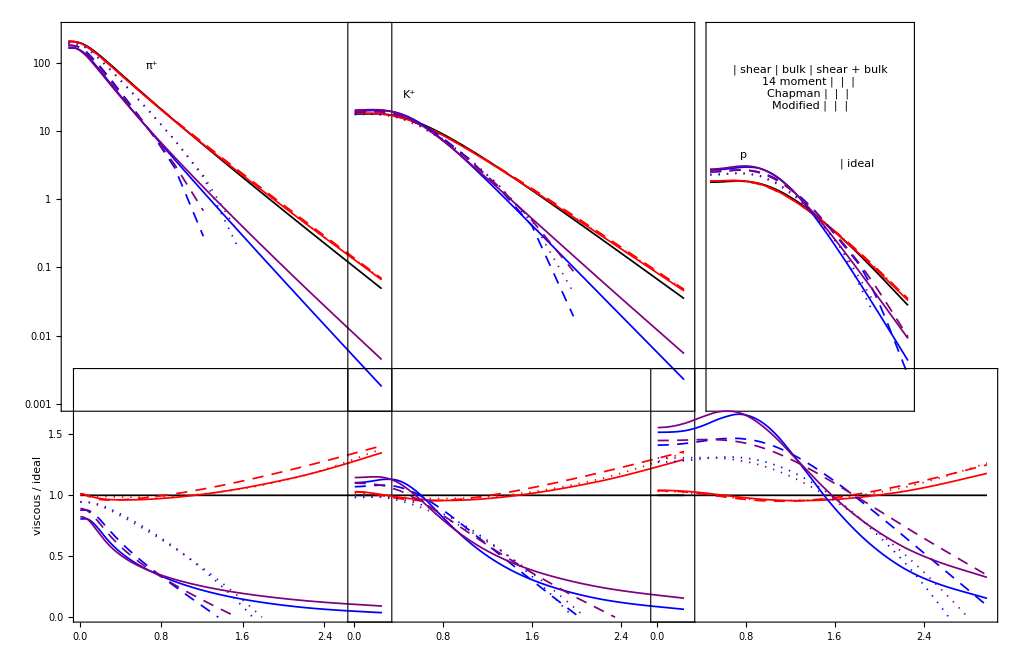
-Graphics-p_T (GeV)

```mathematica
SetDirectory@NotebookDirectory[];

pion = {idealπ,shear14π,shearCEπ,shearmodπ,bulk14π,bulkCEπ,bulkmodπ,shearbulk14π,shearbulkCEπ,shearbulkmodπ};
kaon= {idealK,shear14K,shearCEK,shearmodK,bulk14K,bulkCEK,bulkmodK,shearbulk14K,shearbulkCEK,shearbulkmodK};
proton={idealp,shear14p,shearCEp,shearmodp,bulk14p,bulkCEp,bulkmodp,shearbulk14p,shearbulkCEp,shearbulkmodp};

ratiopion = {ratioidealπ,ratioshear14π,ratioshearCEπ,ratioshearmodπ,ratiobulk14π,ratiobulkCEπ,ratiobulkmodπ,ratioshearbulk14π,ratioshearbulkCEπ,ratioshearbulkmodπ};
ratiokaon= {ratioidealK,ratioshear14K,ratioshearCEK,ratioshearmodK,ratiobulk14K,ratiobulkCEK,ratiobulkmodK,ratioshearbulk14K,ratioshearbulkCEK,ratioshearbulkmodK};
ratioproton={ratioidealp,ratioshear14p,ratioshearCEp,ratioshearmodp,ratiobulk14p,ratiobulkCEp,ratiobulkmodp, ratioshearbulk14p,ratioshearbulkCEp,ratioshearbulkmodp};

(*ratiopionplot=ListPlot[ratiopion,PlotRange->{{0.00,3.0},{0,1.8}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->200,AspectRatio->0.75,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];
ratiokaonplot=ListPlot[ratiokaon,PlotRange->{{0.00,3.0},{0,1.8}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->200,AspectRatio->0.75,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];
ratioprotonplot=ListPlot[ratioproton,PlotRange->{{0.00,3.0},{0,1.8}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->200,AspectRatio->0.75,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];*)
spectra=Panel[GraphicsGrid[{{

ListLogPlot[pion,PlotRange->{{0.0,3},{1.*10^-3,300}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{dNticks,dNticksnone},{pTticksnone,All}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendπ,{0.8,4.5}]}, ImagePadding->{{a,b},{Automatic,Automatic}}],

ListLogPlot[kaon,PlotRange->{{0.005,3.0},{1.*10^-3,300}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{dNticksnone,dNticksnone},{pTticksnone,All}},Joined->True,BaseStyle->{FontSize->14},InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendK,{0.5,3.5}]},ImagePadding->{{a,b},{Automatic,Automatic}}],

ListLogPlot[proton,PlotRange->{{0.005,3.0},{1.*10^-3,300}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{dNticksnone,dNticks},{pTticksnone,All}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendp,{0.5,1.5}],Inset[legenddf,{1.5,3.75}],Inset[legendideal,{2.2,1.2}]},ImagePadding->{{a,b},{Automatic,Automatic}}]},

{ListPlot[ratiopion,PlotRange->{{0.0,3},{0,2}},Frame->True,FrameStyle->Black,FrameLabel->{"",Style["viscous / ideal",FontSize->18,FontFamily->"Arial",Black]},FrameTicks->{{ratioticks,ratioticksnone},{Automatic,pTticksnone}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->0.75,PlotStyle->style, ImagePadding->{{a,b},{Automatic,Automatic}}],

ListPlot[ratiokaon,PlotRange->{{0.005,3.0},{0,2}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{ratioticksnone,ratioticksnone},{True,pTticksnone}},Joined->True,BaseStyle->{FontSize->14},InterpolationOrder->2,ImageSize->450,AspectRatio->0.75,PlotStyle->style,ImagePadding->{{a,b},{Automatic,Automatic}}],

ListPlot[ratioproton,PlotRange->{{0.005,3.0},{0,2}},Frame->True,FrameStyle->Black,FrameLabel->{"",""},FrameTicks->{{ratioticksnone,ratioticks},{True,pTticksnone}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->0.75,PlotStyle->style,ImagePadding->{{a,b},{Automatic,Automatic}}]}


},Spacings->{-116,-200},PlotLabel->Style["(dN/(2  π SubscriptBox[p, T] SubscriptBox[dp, T] dy))_(|_(y = 0))",FontSize->26,FontFamily->"Arial",Black]],{Style["p_T (GeV)",FontFamily->"Arial",FontSize->18]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]

Export["modified_spectra2_500MeV.pdf",spectra];
```